Lots of buzz and energy about Frobenius and his method. Probably more than the average person can put up with. Problems 5, 7, 9, 11, 15, 17 and 19 were worked straightforwardly without resorting to Frobenius, (and 13 could have been).

The following example is found at https : // wps.prenhall.com/wps/media/objects/884/905578/Assignment8_ 2 _V5.pdf. It seems to work for certain equations, and I keep it here for general interest. It does not work on problem 9, however. Reading the included comments may give insight on where it can be expected to work.

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=2 x^2(x+1)y''[x]+3x(x+1)^3 y'[x]-(1-x^2)y[x]==0;
```

The first step is to verify that x=0 is in fact a regular singular point of this equation. This is done by dividing through by the leading coefficient, which is 2 x^2(x+1). This will put the equation in standard form.

```mathematica
y''[x]+(3x(x+1)^3)/(2 x^2(x+1))y'[x]-(1-x^2)/(2 x^2(x+1))y[x]==0;
```

The standard form, shown in numbered line (1) on p. 180, includes a 1/xsub-term for the y'[x] term and a 1/x^2sub-term for the y[x] term. Thus of the remainder of the terms, called p[x] and q[x], the p[x] will be the coefficient for the y' and the q[x] will be the coefficient for the y.

```mathematica
q[x_]=Simplify[-(1-x^2)/(2(x+1))]
```

1/2 (-1+x)

```mathematica
p[x_]=Simplify[(3 (1+x)^2)/2]
```

3/2 (1+x)^2

Taking a good look at the two declarations above, I see that neither one has any x^-m factor in it. This may be necessary for the present example to work. Now to set the number of terms in the series.

```mathematica
n=7;
```

Expand p[x] in a Maclaurin series

```mathematica
pseries=Series[p[x]/x,{x,0,n}]//Normal
```

3+3/(2 x)+(3 x)/2

and also q[x]

```mathematica
qseries=Series[q[x]/x^2,{x,0,n}]//Normal
```

-1/(2 x^2)+1/(2 x)

The first step in making a generic Frobenius series is the following

```mathematica
coeffs=Array[c,n,0];
```

Another component is determined by

```mathematica
lotsofxpowers=Table[x^(r+j),{j,0,2n}];
```

And a third necessary component comes from

```mathematica
xpowers=Table[x^(r+j),{j,0,n-1}];
```

Stirring and gelling the series is accomplished by

```mathematica
y=coeffs.xpowers;
```

The first derivative of the series will be needed

```mathematica
yprime=D[y,x]
```

r x^(-1+r) c[0]+(1+r) x^r c[1]+(2+r) x^(1+r) c[2]+(3+r) x^(2+r) c[3]+(4+r) x^(3+r) c[4]+(5+r) x^(4+r) c[5]+(6+r) x^(5+r) c[6]

Note above that the largest minus exponent in yprime is x^-1. Now to find the second derivative also

```mathematica
y2prime=D[y,{x,2}]
```

(-1+r) r x^(-2+r) c[0]+r (1+r) x^(-1+r) c[1]+(1+r) (2+r) x^r c[2]+(2+r) (3+r) x^(1+r) c[3]+(3+r) (4+r) x^(2+r) c[4]+(4+r) (5+r) x^(3+r) c[5]+(5+r) (6+r) x^(4+r) c[6]

Note above that the largest minus exponent in y2prime is x^-2. The differential equation itself is the next to be created. Because of the limited presence of minus exponents on x, multiplying through by x^2 here normalizes the series so that the lowest order term appearing will be x^r.

```mathematica
x^2*(y2prime+pseries*yprime+qseries*y)//Expand;
```

The series will adopt an appearance of order after executing the following

```mathematica
lhs=Collect[%,lotsofxpowers]
```

x^r (-c[0]/2+1/2 r c[0]+r^2 c[0])+x^(1+r) (c[0]/2+3 r c[0]+c[1]+5/2 r c[1]+r^2 c[1])+x^(2+r) (3/2 r c[0]+(7 c[1])/2+3 r c[1]+(9 c[2])/2+9/2 r c[2]+r^2 c[2])+x^(3+r) ((3 c[1])/2+3/2 r c[1]+(13 c[2])/2+3 r c[2]+10 c[3]+13/2 r c[3]+r^2 c[3])+x^(4+r) (3 c[2]+3/2 r c[2]+(19 c[3])/2+3 r c[3]+(35 c[4])/2+17/2 r c[4]+r^2 c[4])+x^(5+r) ((9 c[3])/2+3/2 r c[3]+(25 c[4])/2+3 r c[4]+27 c[5]+21/2 r c[5]+r^2 c[5])+x^(8+r) (9 c[6]+3/2 r c[6])+x^(7+r) ((15 c[5])/2+3/2 r c[5]+(37 c[6])/2+3 r c[6])+x^(6+r) (6 c[4]+3/2 r c[4]+(31 c[5])/2+3 r c[5]+(77 c[6])/2+25/2 r c[6]+r^2 c[6])

Note above that Collect has ordered the terms so that the x^r term comes first. This may not always be the case, and if it is not, it will affect the following steps. A necessary preliminary step to finding the indicial roots is

```mathematica
firstcoeff=lhs[[1,2]]
```

-c[0]/2+1/2 r c[0]+r^2 c[0]

Note two things about firstcoeff above. It contains elements of r, and it contains a single constant parameter, here c[0]. Both of these characteristics are needed to make the example work. To reveal the roots, set the above expression to zero and solve as follows.

```mathematica
indroots=Solve[firstcoeff==0,r];
```

Order the roots by size

```mathematica
maxroot=Max[r/.indroots]
```

1/2

```mathematica
minroot=Min[r/.indroots]
```

-1

The next step is the first in a series of six steps to find the first solution, y_1.

```mathematica
lhsy1=lhs/.r->maxroot;
```

To determine the values of the arbitrary coefficients, a preliminary step is

```mathematica
y1series=lhsy1/x^maxroot//Distribute;
```

followed by the next step, which makes a list of coefficients.

```mathematica
y1seriescoeffs=Take[CoefficientList[y1series,x],n-1];
```

The higher-degree coefficients in terms of C[0] will be found by

```mathematica
y1coeffs=Solve[{y1seriescoeffs==0,c[0]==1}][[1]];
```

At this point the first solution, y_(1,)can be created by

```mathematica
y=Drop[coeffs,-1].Drop[xpowers,-1]
```

x^r c[0]+x^(1+r) c[1]+x^(2+r) c[2]+x^(3+r) c[3]+x^(4+r) c[4]+x^(5+r) c[5]

followed by the final necessary step

```mathematica
y1=Collect[y/.r->maxroot/.y1coeffs,x]
```

√x-(4 x^(3/2))/5+(13 x^(5/2))/28-(134 x^(7/2))/945-(2741 x^(9/2))/332640+(20429 x^(11/2))/772200

To find the second solution, y_2, requires a similar set of six steps.

```mathematica
lhsy2=lhs/.r->minroot;
y2series=lhsy2/x^minroot//Distribute;
y2seriescoeffs=Take[CoefficientList[y2series,x],n-1];
y2coeffs=Solve[{y2seriescoeffs==0,c[0]==1}][[1]];
y=Drop[coeffs,-1].Drop[xpowers,-1];
y2=Collect[y/.r->minroot/.y2coeffs,x]
```

-5+1/x+4 x-(28 x^2)/9+(64 x^3)/45-(376 x^4)/1575

And now the two solutions, y_1 and y_2, are plotted. Note that the roots to the equations are not those found above. Those roots were indicial roots, not roots to the actual ODE solution equation.

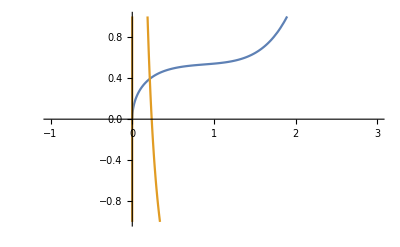

```mathematica
Plot[{y1,y2},{x,-1,3},PlotRange->{{-1,3},{-1,1}}]
```

If I want to find the actual roots to the two solutions, I can.

```mathematica
FindRoot[y1,{x,0}]
```

{x→0.}

```mathematica
FindRoot[y2,{x,0.2}]
```

{x→0.237723}

If I task WolframAlpha with the problem, it tells me it is Sturm-Liouville, but doesn’t solve it, only gives some possible plots. Taking this as a cue, I could do (for y1)

```mathematica
Clear["Global`*"]
```

```mathematica
eqn2=2 x^2(x+1)y''[x]+3x(x+1)^3 y'[x]-(1-x^2)y[x]==0;
ics={y[0.6]==0.51,y'[0.13]==1};
num=First[y/.NDSolve[{eqn2,ics},y,{x,0.01,1}]]
```

InterpolatingFunction[{{0.01, 1.}}, <>]

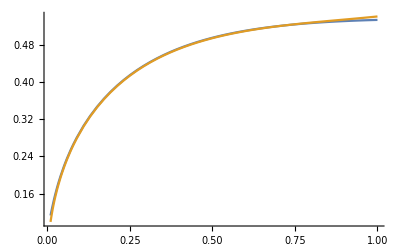

```mathematica
Plot[{num[x],√x-(4 x^(3/2))/5+(13 x^(5/2))/28-(134 x^(7/2))/945-(2741 x^(9/2))/332640+(20429 x^(11/2))/772200},{x,0.01,1}]
```

showing the y1 solution just starting to peel away above the interpolated function at x=1.
I have not been successful in checking the solutions y1 and y2, though I have tried a couple of different ways.
And the equation seems resistant to DSolve. For instance, the straightforward attempt below only returns an uninformative briar patch of formal characters.

```mathematica
Clear["Global`*"]
```

```mathematica
eqn2=2 x^2(x+1)y''[x]+3x(x+1)^3 y'[x]-(1-x^2)y[x]==0;
```

```mathematica
sol=DSolve[eqn2,y,x]
```

{{y→DifferentialRoot[Function[{y,x},{(-1+x) y[x]+3 x (1+x)^2 y'[x]+2 x^2 y''[x]==0,y[1]==C[1],y'[1]==C[2]}],«»]}}

2 - 13 Frobenius method
Find a basis of solutions by the Frobenius method. Try to identify the series as expansions of known functions.

3.  x y'' + 2 y' + x y = 0

```mathematica
Clear["Global`*"]
```

$1. Working through the long and involved Frobenius method described in the text and s.m.. The Hold command does not seem to work as I would like, it gets in the way. I don’t have nomenclature to designate a Mathematica pseudosum.

```mathematica
e7=f[x_]=Subscript[a, m] x^(m+r)
```

x^(m+r) a_m

$2. What is meant by above is the Sum[a_m x^(m+r),{m,0,∞}]

```mathematica
e8=f'[x]
```

(m+r) x^(-1+m+r) a_m

```mathematica
e9=f''[x]
```

(-1+m+r) (m+r) x^(-2+m+r) a_m

```mathematica
e10=x^2 f''[x]+2 x f'[x]+x^2 f[x]==0
```

2 (m+r) x^(m+r) a_m+(-1+m+r) (m+r) x^(m+r) a_m+x^(2+m+r) a_m==0

$3. Above: The exponential powers of the first two ‘x’ factors are equal, but the third is two higher. Since these represent infinite sums, it would not affect their individual (or collective) summations if the indices were adjusted to all match. As the s.m. suggested, this can be accomplished by effectively subtracting 2 from the power of x in the third occurence of that variable. This would make the third pseudosum start at 2 (instead of 0) to compensate. As for a_m, that element would be changed to a_(m-2) in order to have it start at the same place as before the change.

```mathematica
e11=e10/.(x^(2+m+r) Subscript[a, m])->(x^(m+r) Subscript[a, m-2])
```

x^(m+r) a_(-2+m)+2 (m+r) x^(m+r) a_m+(-1+m+r) (m+r) x^(m+r) a_m==0

$4. Above: Last reminder of the form change. Having all the factors mix together should not invalidate anything. However, if I find myself in a position where I want to assign 0 or 1 to the index m, the coefficient m_(-2+m) will drop out.

```mathematica
e12=Expand[e11]
```

x^(m+r) a_(-2+m)+m x^(m+r) a_m+m^2 x^(m+r) a_m+r x^(m+r) a_m+2 m r x^(m+r) a_m+r^2 x^(m+r) a_m==0

```mathematica
e13=Simplify[e12]
```

x^(m+r) (a_(-2+m)+(m+m^2+r+2 m r+r^2) a_m)==0

$5. Below: The indicial equation. (What makes it the indicial equation is setting m=0.) In transferring from above, the factor a_(-2+m) was ignored.

```mathematica
e14=Solve[m+m^2+r+2 m r+r^2==0,r]/.m->0
```

{{r→-1},{r→0}}

$6. Above: The sol’n of the indicial equation. The s.m. wants to look at the larger root first, r=0. Where am I? After I equalized powers of x, expanded, and simplified, I got e13. Now I will look at e13 again, but with r  evaluated.

```mathematica
e15=e13/.{r->0}
```

x^m (a_(-2+m)+(m+m^2) a_m)==0

```mathematica
e16=Solve[(Subscript[a, -2+m]+(m+m^2) Subscript[a, m])==0,Subscript[a, m]]/.{m->1,Subscript[a, -2+m]->0}
```

{{a_1→0}}

$7. Making m=1 in the above allows the finding of a_1. Since m<2, the coefficient a_(-2+m) will be zero.

```mathematica
e17=e13/.{Subscript[a, -2+m]->0,r->0}
```

(m+m^2) x^m a_m==0

$8. Above: Getting a look at the heart of the equation updated.

```mathematica
A={};
Do[A=Union[A,Solve[(Subscript[a, -2+m]+(m+m^2) Subscript[a, m])==0,Subscript[a, m]]],{m,2,7}];A
```

{{a_2→-a_0/6},{a_3→-a_1/12},{a_4→-a_2/20},{a_5→-a_3/30},{a_6→-a_4/42},{a_7→-a_5/56}}

$9. What the above set A does not include is the factor a_0 x^0. The s.m recommends assigning the value 1 to a_0, and this will be added when the opportunity presents. The starting value of m is 2, because that is the lowest value for which a_(-2+m) has meaning. There is no assigned value for a_1 yet. But now everything has a value based on either a_0 or a_1.

```mathematica
B={};
Eliminate[{Subscript[a, 4]==-Subscript[a, 2]/20,Subscript[a, 2]==-Subscript[a, 0]/6},Subscript[a, 2]]
```

120 a_4==a_0

```mathematica
Eliminate[{Subscript[a, 6]==-Subscript[a, 4]/42,120 Subscript[a, 4]==Subscript[a, 0]},Subscript[a, 4]]
```

-5040 a_6==a_0

```mathematica
Eliminate[{Subscript[a, 5]==-Subscript[a, 3]/30,Subscript[a, 3]==-Subscript[a, 1]/12},Subscript[a, 3]]
```

360 a_5==a_1

```mathematica
Eliminate[{Subscript[a, 7]==-Subscript[a, 5]/56,360 Subscript[a, 5]==Subscript[a, 1]},Subscript[a, 5]]
```

-20160 a_7==a_1

```mathematica
B={{Subscript[a, 0]->1},{Subscript[a, 2]->-Subscript[a, 0]/6},{Subscript[a, 3]->-Subscript[a, 1]/12},{Subscript[a, 4]->Subscript[a, 0]/120},{Subscript[a, 5]->Subscript[a, 1]/360},{Subscript[a, 6]->-Subscript[a, 0]/5040},{Subscript[a, 7]->-Subscript[a, 1]/20160}}
```

{{a_0→1},{a_2→-a_0/6},{a_3→-a_1/12},{a_4→a_0/120},{a_5→a_1/360},{a_6→-a_0/5040},{a_7→-a_1/20160}}

```mathematica
cs={2!,3!,4!,5!,6!,7!,8!}
```

{2,6,24,120,720,5040,40320}

```mathematica
B[[3]]=B[[3]]/.Subscript[a, 2]/120->Subscript[a, 1]/24
```

{a_3→-a_1/12}

```mathematica
B[[4]]=B[[4]]/.Subscript[a, 2]->Subscript[a, 0]
```

{a_4→a_0/120}

```mathematica
B[[5]]=B[[5]]/.Subscript[a, 3]->Subscript[a, 1]
```

{a_5→a_1/360}

```mathematica
B[[6]]=B[[6]]/.Subscript[a, 4]->Subscript[a, 0]
```

{a_6→-a_0/5040}

```mathematica
B[[7]]=B[[7]]/.Subscript[a, 5]->Subscript[a, 1]
```

{a_7→-a_1/20160}

```mathematica
e19=TableForm[Table[{m,Subscript[a, m],B[[m]]},{m,2,7}],TableHeadings->{{},{"m","a_m ","B[m] ","a_1"}}]
```

| m | a_m  | B[m]  | a_1
 | 2 | a_2 | a_2→-a_0/6 | 
 | 3 | a_3 | a_3→-a_1/12 | 
 | 4 | a_4 | a_4→a_0/120 | 
 | 5 | a_5 | a_5→a_1/360 | 
 | 6 | a_6 | a_6→-a_0/5040 | 
 | 7 | a_7 | a_7→-a_1/20160 |

$10. There are two series. Let me see if I can separate them:

```mathematica
B1={B[[3,1,2]],B[[5,1,2]],B[[7,1,2]]}
```

{-a_1/12,a_1/360,-a_1/20160}

$11. There is a problem with B1. However, since it will not be used, there is no need to investigate it.

```mathematica
B2={B[[1,1,2]],B[[2,1,2]],B[[4,1,2]],B[[6,1,2]]}
```

{1,-a_0/6,a_0/120,-a_0/5040}

```mathematica
e20=TableForm[Table[{m,B2[[m]]},{m,1,4}],TableHeadings->{{},{"term","B2[m] "}}]
```

| term | B2[m] 
 | 1 | 1
 | 2 | -a_0/6
 | 3 | a_0/120
 | 4 | -a_0/5040

```mathematica
y1=Sum[B2[[s]] x^(2(s-1)),{s,1,4}]
```

1-(x^2 a_0)/6+(x^4 a_0)/120-(x^6 a_0)/5040

$12. To do as s.m., a_0 was assigned a value of 1. Then y1=1-x^2/(3!)+x^4/(5!)-x^6/(7!)

$13. Below is shown the definition version of what will now be called y1. It agrees with the text answer for y_1.

```mathematica
Series[Sin[x]/x, {x,0,4}]
```

1-x^2/6+x^4/120+O[x]^5

$14. To get the second sol’n in the basis, y2, it is recommended by the s.m. to march off and do reduction of order, covered in Sec 2.1 of the text. From that perspective it is deemed important to put the original equation into standard form,

```mathematica
e21={y''[x]+2/x y'[x]+ y[x]==0}
```

{y[x]+(2 y'[x])/x+y''[x]==0}

```mathematica
p[x_]=2/x
```

2/x

```mathematica
-Integrate[p[x], x,GenerateConditions->True]
```

-2 Log[x]

$15. Above: Mathematica does not bother to show that the correct answer involves Abs[x]. The plot below shows the difference. This doesn’t seem to affect this particular answer, but the omission is somewhat disturbing.

```mathematica
plot1=Plot[-2 Log[x],{x,-2,2},PlotStyle->Yellow,ImageSize->250];
```

```mathematica
plot2 =Plot[-2Log[Abs[x]],{x,-2,2},PlotStyle->{Blue,Thickness[0.01]}];
```

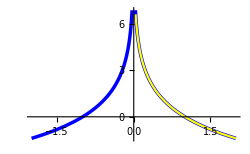

```mathematica
Show[plot2,plot1]
```

$16. Putting the integral into another form.

```mathematica
Exp[-Integrate[p[x], x]]
```

1/x^2

$17. The expression: U=1/y_1^2 ⅇ^(-∫pⅆx) is from section 2.1, p.52, where one sol’n to a homogeneous linear ODE with constant coefficents is already known and you are tracking down the other part of the basis. Putting it to use,

```mathematica
capU=Exp[-Integrate[p[x], x]]/(Sin[x]/x)^2
```

Csc[x]^2

```mathematica
smallu=Integrate[capU,x]
```

-Cot[x]

```mathematica
y2=smallu Sin[x]/x
```

-Cos[x]/x

$18. The s.m. points out that since it is a combo of y1 and y2 and there are arbitrary coefficients involved, the minus sign on y2 is not necessary, and the version shown in the answer section (no minus sign) can be claimed.

5.  x y'' + (2 x + 1) y' + (x + 1) y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
e1={x y''[x]+(2 x+1) y'[x]+(x+1) y[x]==0}
```

{(1+x) y[x]+(1+2 x) y'[x]+x y''[x]==0}

```mathematica
sol=DSolve[e1,y,x]
```

{{y→Function[{x},ⅇ^-x C[1]+ⅇ^-x C[2] Log[x]]}}

```mathematica
e1/.sol//Simplify
```

{{True}}

Mathematica can solve this one without all the Frobenius gingerbread. It should be noted that the two parts (terms) of the sol’n shown in green above are considered two separate sol’ns, y1 and y2. This was the same case with the first problem, no. 3. In the text answer C[1] and C[2] are equal to 1. The answer agrees with that of the text.

7.  y'' + (x - 1) y = 0

Also with this problem I attempt to skip the Frobenius method in favor of a direct assault.

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=y''[x] + (x - 1) y[x]== 0
```

(-1+x) y[x]+y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},AiryAi[-(-1)^(1/3) (1-x)] C[1]+AiryBi[-(-1)^(1/3) (1-x)] C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
FindRoot[AiryAi[-(-1)^(1/3) (1-x)] +AiryBi[-(-1)^(1/3) (1-x)],{x,.1}]
```

{x→-0.845332+3.19621 ⅈ}

Though Mathematica finds a pair of apparently viable solutions, dealing with Airy is not that easy for me. To plot it, some kind of numericalization seems required, one example being

```mathematica
solN=First[y/.NDSolve[{eqn,y[0]==0,y'[0]==1},y,{x,0,5}]]
```

InterpolatingFunction[{{0., 5.}}, <>]

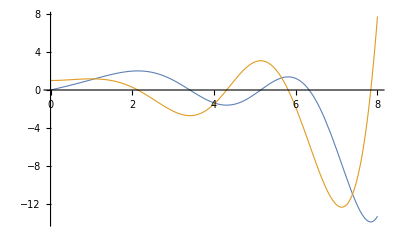

```mathematica
Plot[{solN[x],solN'[x]},{x,0,8},PlotStyle->Thickness[0.002]]
```

And a parametric plot suggested by the WolframAlpha result,

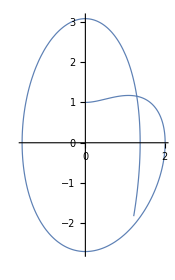

```mathematica
ParametricPlot[{solN[x],solN'[x]},{x,0,6},ImageSize->175,PlotStyle->Thickness[0.005]
]
```

As a matter of interest, I experimented with the Cocalc site, (https://cocalc.com), where Sage leverages Maxima to get a friendlier Bessel solution with the command: sage: desolve(diff(y,x,2)+(x-1)*y==0,y,contrib_ode=True,show_method=True)

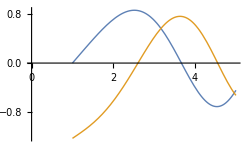

```mathematica
Plot[{√(x-1)BesselJ[1/3,2/3(x-1)^(3/2)],√(x-1)BesselY[1/3,2/3(x-1)^(3/2)]},{x,0,5},ImageSize->250,PlotStyle->Thickness[0.004]]
```

One obvious advantage of the Bessel version is that it is not necessary to particularize it in order to get a plot. At the site https://mathematica.stackexchange.com/questions/183164/ndeigenvalues-vs-findroot-for-finding-the-eigenvalues-of-airy-equation/183276#183276, in the answer of Bill Watts, are some functions that convert Airy to Bessel. P is for positive x, and M is for minus x.

```mathematica
AiryToBesP={AiryAi[x_]->(1/3)*Sqrt[x]*(BesselI[-3^(-1),(2/3)*x^(3/2)]-BesselI[1/3,(2/3)*x^(3/2)]),AiryBi[x_]->Sqrt[x/3]*(BesselI[-3^(-1),(2/3)*x^(3/2)]+BesselI[1/3,(2/3)*x^(3/2)])};
AiryToBesM={AiryAi[x_]->(1/3)*Sqrt[-x]*(BesselJ[-3^(-1),(2/3)*Sqrt[-x]^3]+BesselJ[1/3,(2/3)*Sqrt[-x]^3]),AiryBi[x_]->Sqrt[-x/3]*(BesselJ[-3^(-1),(2/3)*Sqrt[-x]^3]-BesselJ[1/3,(2/3)*Sqrt[-x]^3])};
```

Carrying on with the above choice of positive x,

```mathematica
y[x_]=solN[x]/.AiryToBesP//Simplify
```

InterpolatingFunction[{{0., 5.}}, <>][x]

```mathematica
Plot[{y[x],y'[x]},{x,0,8},PlotStyle->Thickness[0.002]]
```

-Graphics-

The above looks like the previous plot of solN, except that it was not necessary to use NDSolve, which could be an advantage, as it seems to have greater generality.

9.  2 x (x - 1) y'' - (x + 1) y' + y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=2x(x-1)y''[x]-(x+1)y'[x]+y[x]==0
```

y[x]-(1+x) y'[x]+2 (-1+x) x y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},√x C[1]-2 (1+x) C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

It appears that Frobenius’s method is not necessary with this problem. In order to make the green cell match the text answer, I choose C[1]=1 and C[2]=-1/2.

11.  x y'' + (2 - 2 x) y' + (x - 2) y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=x y''[x]+(2-2x)y'[x]+(x-2)y[x]==0
```

(-2+x) y[x]+(2-2 x) y'[x]+x y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},(ⅇ^x C[1])/x+ⅇ^x C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

Again the Frobenius method is not necessary. To make the green cell match the text answer, I choose C[1] = C[2]=1.

13.  x y'' + (1 - 2 x) y' + (x - 1) y = 0

This is one problem where Frobenius works smoothly. However, I notice now that Frobenius is not necessary, and the solutions pop right out using plain old DSolve.

```mathematica
Clear["Global`*"]
```

```mathematica
e1=x y''[x]+(1- 2 x) y'[x]+(x-1) y[x]==0
```

(-1+x) y[x]+(1-2 x) y'[x]+x y''[x]==0

```mathematica
e2=x e1
```

x ((-1+x) y[x]+(1-2 x) y'[x]+x y''[x]==0)

```mathematica
e3=x ((-1+x) y[x]+(1-2 x) y'[x]+x y''[x])==0
```

x ((-1+x) y[x]+(1-2 x) y'[x]+x y''[x])==0

```mathematica
e4=Expand[e3]
```

-x y[x]+x^2 y[x]+x y'[x]-2 x^2 y'[x]+x^2 y''[x]==0

```mathematica
e5=Collect[e4,{y''[x],y'[x],y[x]}]
```

(-x+x^2) y[x]+(x-2 x^2) y'[x]+x^2 y''[x]==0

x b(x) must equal (x-2 x^2) and c(x) y must equal (-x+x^2). So b(x) equals (1-2x). To find out b_0 and c_0, it is necessary to expand them.

```mathematica
e6=Series[1-2x,{x,0,2}]
```

1-2 x+O[x]^3

So b_0=1.

```mathematica
e7=Series[-x+x^2,{x,0,2}]
```

-x+x^2+O[x]^3

Because there is no constant term in the expansion of c(x), the s.m. tells me that c_0=0.

The sol’n series will look like:

```mathematica
y1[x_]=Subscript[a, m] x^(m+r)
```

x^(m+r) a_m

```mathematica
y1'[x]
```

(m+r) x^(-1+m+r) a_m

```mathematica
y1''[x]
```

(-1+m+r) (m+r) x^(-2+m+r) a_m

Since I know b(x) and c(x) and b_0 and c_0, I can write the indicial equation.

```mathematica
e8=Solve[r(r-1)+1 r +0==0,r]
```

{{r→0},{r→0}}

Mathematica is telling me it is a double root. Now I can write the original equation,

```mathematica
e9=x y1''[x]+(1- 2 x) y1'[x]+(x-1) y1[x]==0
```

(-1+m+r) (m+r) x^(-1+m+r) a_m+(m+r) (1-2 x) x^(-1+m+r) a_m+(-1+x) x^(m+r) a_m==0

```mathematica
e10=e9/.{r->0}
```

(-1+m) m x^(-1+m) a_m+m (1-2 x) x^(-1+m) a_m+(-1+x) x^m a_m==0

```mathematica
e11=Collect[e10,(-1+m)]
```

m x^(-1+m) a_m+(-1+m) m x^(-1+m) a_m-x^m a_m-2 m x^m a_m+x^(1+m) a_m==0

The five factors above are the same factors as in the s.m.

```mathematica
e12=Collect[e11,{x^(-1+m),x^m,x^(1+m)}]
```

m^2 x^(-1+m) a_m+x^(1+m) a_m+x^m (-a_m-2 m a_m)==0

This also matches, at the place where the powers are adjusted.

```mathematica
e13=e12/.{(m^2 x^(-1+m) Subscript[a, m])->((s+1)^2 Subscript[a, s+1] x^s),(x^(1+m) Subscript[a, m])->(Subscript[a, s-1] x^s),(x^m (-Subscript[a, m]-2 m Subscript[a, m]))->(-(2 s+1)Subscript[a, s] x^s)}
```

x^s a_(-1+s)+(-1-2 s) x^s a_s+(1+s)^2 x^s a_(1+s)==0

The powers are adjusted. If shown as real sums, the third factor (sum) would be {s,-1,∞}, the second {s,0,∞}, and the first {s,1,∞}.

For the case of s=-1, only the third factor would work, fitting into that index range.

```mathematica
e14=Solve[(1+s)^2 x^s Subscript[a, 1+s]==0,Subscript[a, s+1]]/.s->-1
```

{{a_0→0}}

In the case of s=0, both second and third factors can accommodate.

```mathematica
e15=Solve[(-1-2 s) x^s Subscript[a, s]+(1+s)^2 x^s Subscript[a, 1+s]==0,Subscript[a, s]]/.s->0
```

{{a_0→a_1}}

In the case of s>0, all three factors can accommodate.

```mathematica
e16=Solve[x^s Subscript[a, -1+s]+(-1-2 s) x^s Subscript[a, s]+(1+s)^2 x^s Subscript[a, 1+s]==0,Subscript[a, s]]/.s->1
```

{{a_1→1/3 (a_0+4 a_2)}}

```mathematica
e17=Solve[Subscript[a, 1]==1/3 (Subscript[a, 0]+4 Subscript[a, 2]),Subscript[a, 2]]/.Subscript[a, 1]->Subscript[a, 0]
```

{{a_2→a_0/2}}

```mathematica
e18=Solve[x^s Subscript[a, -1+s]+(-1-2 s) x^s Subscript[a, s]+(1+s)^2 x^s Subscript[a, 1+s]==0,Subscript[a, s+1]]
```

{{a_(1+s)→(-a_(-1+s)+a_s+2 s a_s)/(1+s)^2}}

```mathematica
e19=e18/.{s->1,Subscript[a, 0]->1}
```

{{a_2→1/4 (-a_0+3 a_1)}}

```mathematica
loc={};
e20=Do[loc=Union[loc,Solve[x^s Subscript[a, -1+s]+(-1-2 s) x^s Subscript[a, s]+(1+s)^2 x^s Subscript[a, 1+s]==0,Subscript[a, s+1]]/.{Subscript[a, 0]->1,Subscript[a, 1]->1}],{s,1,4}];loc
```

This marks the point where values for both a_0 and a_1 are shown as assigned.

{{a_2→1/2},{a_3→1/9 (-1+5 a_2)},{a_4→1/16 (-a_2+7 a_3)},{a_5→1/25 (-a_3+9 a_4)}}

```mathematica
e21=Solve[Subscript[a, 3]==1/9 (-1+5 Subscript[a, 2]),Subscript[a, 3]]/.Subscript[a, 2]->1/2
```

{{a_3→1/6}}

```mathematica
e22=Solve[Subscript[a, 4]==1/16 (-Subscript[a, 2]+7 Subscript[a, 3]),Subscript[a, 4]]/.{Subscript[a, 2]->1/2,Subscript[a, 3]->1/6}
```

{{a_4→1/24}}

```mathematica
e23=Solve[Subscript[a, 5]==1/25 (-Subscript[a, 3]+9 Subscript[a, 4]),Subscript[a, 5]]/.{Subscript[a, 2]->1/2,Subscript[a, 3]->1/6,Subscript[a, 4]->1/24}
```

{{a_5→1/120}}

```mathematica
e24=cs={2!,3!,4!,5!,6!,7!,8!}
```

{2,6,24,120,720,5040,40320}

```mathematica
e25=y1[x_]=Sum[Subscript[a, m] x^m,{m,0,4}]
```

a_0+x a_1+x^2 a_2+x^3 a_3+x^4 a_4

In e20 I said that a_0=a_1=1. Thus y1=1+x+x^2/(2!)+x^3/(3!)+x^4/(4!)+· · · Looks like ⅇ^x.

```mathematica
Subscript[y, 1]=Series[ⅇ^x,{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

The green cell above matches the text answer for y_1. It is still necessary to get a second solution. Again, the method is reduction of order. The first step is to put the equation into standard form.

```mathematica
e26=1/x(-y[x]+x y[x]+y'[x]-2 x y'[x]+x y''[x])==0
```

(-y[x]+x y[x]+y'[x]-2 x y'[x]+x y''[x])/x==0

```mathematica
e28=Collect[e26,{y''[x],y'[x],y[x]}]
```

((-1+x) y[x])/x+((1-2 x) y'[x])/x+y''[x]==0

```mathematica
e29=p[x_]=(1-2 x)/x
```

(1-2 x)/x

Following the procedure for reduction of order,

```mathematica
e30=-Integrate[p[x],x]
```

2 x-Log[x]

Using log identity, this is

```mathematica
e31=e30/.-Log[x]->Log[1/x]
```

2 x+Log[1/x]

Again, Mathematica forgot to use the Abs function when integrating a fraction.

```mathematica
e32=Exp[e31]
```

ⅇ^(2 x)/x

Continuing to follow the reduction recipe, we have our big U and little u. As shown in s.m.,

```mathematica
e33=bigU[x_]=1/((ⅇ^x)^2)(ⅇ^(2 x)/x)
```

1/x

And as for little u,

```mathematica
e34=u[x_]=Integrate[bigU[x],x]
```

Log[x]

Again, should be Abs

```mathematica
y2=u[x] ⅇ^x
```

ⅇ^x Log[x]

The green cell above matches the text answer for y_2.

15 - 20 Hypergeometric ODE
Find a general solution in terms of hypergeometric functions.

15.  2 x (1 - x) y'' - (1 + 6 x) y' - 2 y = 0

```mathematica
Clear["Global`*"]
```

Sometimes Mathematica expresses its output as Hypergeometric. But if it doesn’t, I’m not going to feel bad about it. In fact the plain dealing output below is better, in my opinion. Anyway, I  need to try to implement a translation of Hypergeometric in assessing the answer.

```mathematica
eqn=2 x (1 - x) y''[x] - (1 + 6 x) y'[x] - 2 y[x] == 0
```

-2 y[x]-(1+6 x) y'[x]+2 (1-x) x y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},(x^(3/2) C[1])/(1-x)^(5/2)+(2 (-√(1-x)+4 √(1-x) x+3 x^(3/2) ArcSin[√x]) C[2])/(3 √(1-x) (-1+x)^2)]}}

```mathematica
eqn/.sol//Simplify
```

{True}

Though the format differs slightly, it is not too hard to interpret the text answer in the syntax native to Mathematica.

```mathematica
x^(3/2)Hypergeometric2F1[5/2,5/2,5/2,x]
```

x^(3/2)/(1-x)^(5/2)

```mathematica
Hypergeometric2F1[1,1,-1/2,x]
```

Hypergeometric2F1[1,1,-1/2,x]

Mathematica returns what looks like a valid solution. The top pink cell contents, contained in the text answer, matches with the first function, assuming C[1] is assigned the value of 1, but the bottom pink expression, also from the text solution, is returned unevaluated by Mathematica. As an emergency resource, I turn to WolframAlpha for output:

```mathematica
Hypergeometric2F1[1,1,-1/2,x]=(1-4x)/(x-1)^2-(3 x^(3/2)ArcSin[√x])/(√(1-x)(x-1)^2)
```

So with the W|A output I can try

```mathematica
Solve[((2 (-√(1-x)+4 √(1-x) x+3 x^(3/2) ArcSin[√x]) C[2])/(3 √(1-x) (-1+x)^2))-((1-4x)/(x-1)^2-(3 x^(3/2)ArcSin[√x])/(√(1-x)(x-1)^2))==0,C[2]]
```

{{C[2]→(3 √(1-x) (-1+x)^2 ((1-4 x)/(-1+x)^2-(3 x^(3/2) ArcSin[√x])/(√(1-x) (-1+x)^2)))/(2 (-√(1-x)+4 √(1-x) x+3 x^(3/2) ArcSin[√x]))}}

```mathematica
FullSimplify[(3 √(1-x) (-1+x)^2 ((1-4 x)/(-1+x)^2-(3 x^(3/2) ArcSin[√x])/(√(1-x) (-1+x)^2)))/(2 (-√(1-x)+4 √(1-x) x+3 x^(3/2) ArcSin[√x]))]
```

-3/2

So simply by assigning the value -3/2 to the constant C[2], the answers match.

17.  4 x (1 - x) y'' + y' + 8 y = 0

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=4 x (1 - x) y''[x] + y'[x] + 8 y[x] == 0
```

8 y[x]+y'[x]+4 (1-x) x y''[x]==0

```mathematica
sol=DSolve[eqn,y,x]
```

{{y→Function[{x},(1-x)^(5/4) x^(3/4) C[1]-4/15 (5-40 x+32 x^2) C[2]]}}

```mathematica
eqn/.sol//Simplify
```

{True}

To check the answer, I need to convert the text answer to non-Hyper.

```mathematica
x^(3/4)Hypergeometric2F1[7/4,-5/4,7/4,x]
```

(1-x)^(5/4) x^(3/4)

The green cell above matches the text answer, with C[1]=1 and C[2]=-3/4, (assuming the text constants A and B both equal 1).

19.  2(t^2-5t+6)ÿ+(2t-3)ẏ-8y=0

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=2(t^2-5t+6)y''[t]+(2t-3)y'[t]-8y[t]==0
```

-8 y[t]+(-3+2 t) y'[t]+2 (6-5 t+t^2) y''[t]==0

```mathematica
sol=DSolve[eqn, y,t]
```

{{y→Function[{t},((2-t)^(1/4) (-3+t)^(1/4) (-2+t)^(5/4) (-17+6 t) C[1])/(6 (3-t)^(3/4))+(4 (2-t)^(1/4) (-3+t)^(3/4) (111-104 t+24 t^2) C[2])/(5 (3-t)^(3/4) (-2+t)^(1/4))]}}

```mathematica
eqn/.sol//Simplify
```

{True}

Trying to re-express the text answer into a non-Hyper form,

```mathematica
(t-2)^(3/2)Hypergeometric2F1[7/2,-1/2,5/2,t-2]
```

((17-6 t) (-2+t)^(3/2))/(5 √(3-t))

```mathematica
Hypergeometric2F1[2,-2,-1/2,t-2]
```

-111+104 t-24 t^2

I need to try to reconcile Mathematica's answer with that of the text.

```mathematica
Solve[((2-t)^(1/4) (-3+t)^(1/4) (-2+t)^(5/4) (-17+6 t) C[1])/(6 (3-t)^(3/4))-((17-6 t) (-2+t)^(3/2))/(5 √(3-t))==0,C[1]]//Simplify
```

{{C[1]→-(6 (-(-3+t) (-2+t))^(1/4))/(5 (2-t)^(1/4) (-3+t)^(1/4))}}

```mathematica
int=-(6 (-(-3+t) (-2+t))^(1/4))/(5 (2-t)^(1/4) (-3+t)^(1/4))
```

-(6 ((3-t) (-2+t))^(1/4))/(5 (2-t)^(1/4) (-3+t)^(1/4))

```mathematica
Simplify[((3-t)(-2+t))/((2-t)(-3+t))]
```

1

From the above, I see that the first pair of functions differs only by the arbitrary constant C[1], and that this constant should receive the value of 1.

```mathematica
Solve[(4 (2-t)^(1/4) (-3+t)^(3/4) (111-104 t+24 t^2) C[2])/(5 (3-t)^(3/4) (-2+t)^(1/4))-(-111+104 t-24 t^2)==0,C[2]]
```

{{C[2]→(5 (3-t)^(3/4) (-2+t)^(1/4) (-111+104 t-24 t^2))/(4 (2-t)^(1/4) (-3+t)^(3/4) (111-104 t+24 t^2))}}

```mathematica
Simplify[(3-t)/(-3+t)]
```

-1

```mathematica
Simplify[(-2+t)/(2-t)]
```

-1

```mathematica
Simplify[(-111+104 t-24 t^2)/(111-104 t+24 t^2)]
```

-1

From the above four output cells, I see that the second pair of functions differs only by the assigned value of C[2], which looks like it should get the value of -1, stemming from (-1*-1*-1) = -1.

I therefore conclude that yellow cell equals the sum of the two pinks, and therefore yellow is equivalent to the text answer.